Laboratory #6: Oscilloscopes and Circuits
J.R. Powers-Luhn
NE550, Thursday 17:30-20:30
Partner: Tanner Jacobi
Station: #01

Pre-laboratory Questions

1. Read the laboratory assignment in its entirety before coming to lab.

Check

2. Read the Wikipedia page on oscilloscope (https://en.wikipedia.org/wiki/Oscilloscope).

Check

3. What is the purpose of AC coupling on an oscilloscope?

This presents on the the time-varying portions of the signal, without the DC voltage that this signal might be “riding” on.

4. What is the most common use of an oscilloscope?

According to Wikipedia (https://en.wikipedia.org/wiki/Oscilloscope#Examples_of_use), “[o]ne of the most frequent uses of scopes is troubleshooting malfunctioning electronic equipment.” Using the oscilloscope it is possible to probe in between components in a signal path, comparing the measured output against some expected result. In this way it is possible, via binary troubleshooting, to find the faulty component in 2^-n time, where n is the number of components.

5. In a DMM, the resistance values will change as a function of the current magnitude being measured. Explain why this happens and if this could affect a measured value in a given experiment.

The resistance value changes because the ammeter introduces a series resistor of known size and measures the voltage drop across that resistor in order to calculate current in the circuit. The resistor value is chosen to interfere only minimally with the circuit (i.e. the resistor in the DMM is small compared to the resistance of the circuit being measured), but it must also be sized to produce a measurable voltage drop across the measurement resistor. Because of this compromise, the different resistance values for each setting of the DMM may produce slightly different results.

6. In class we analytically solved the differential equation describing a CR network.
	a. Graphically display via plotting software how the input sinusoidal wave is modified at the output when modifying the input frequency. Plot the cases when the input frequency varies in decades from 10^3-10^7 Hz. Use a time constant of one microsecond, a peak-to-peak input amplitude of two volts, and a time domain covering at least four periods. Put the input and output on a single plot (5 plots total).

```mathematica
Clear[τ,Subscript[V, 0]]
```

Clear::ssym: V_0 is not a symbol or a string.

```mathematica
Subscript[V, 0]=1; (* volts, corresponds to 2V peak-to-peak *)
Subscript[V, in][f_, Subscript[V, 0]_, t_]:=Subscript[V, 0] Sin[2 π f t];
DSolve[{Subscript[V, 0] 2 π f * Cos[2 π f t]==V[t]/τ+V'[t],V[0]==0},V[t],t][[1,1,2]]
```

(20000000 ⅇ^(-t/τ) π τ (-1+ⅇ^(t/τ) Cos[20000000 π t]+20000000 ⅇ^(t/τ) π τ Sin[20000000 π t]))/(1+400000000000000 π^2 τ^2)

```mathematica
Subscript[V, out][f_,Subscript[V, 0]_,t_,τ_]:=(2 ⅇ^(-t/τ) f π τ (-1+ⅇ^(t/τ) Cos[2 f π t]+2 ⅇ^(t/τ) f π τ Sin[2 f π t]))/(1+4 f^2 π^2 τ^2)
```

```mathematica
tau=10*10^-6; (* seconds *)
```

Input frequency: 10^3 Hz:

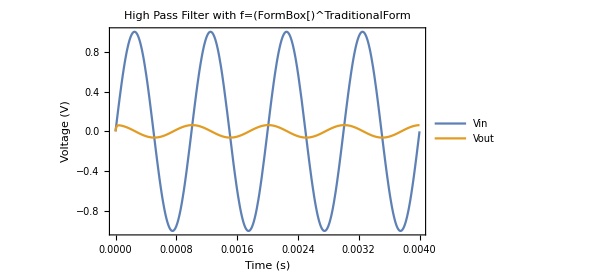

```mathematica
f=10^3;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

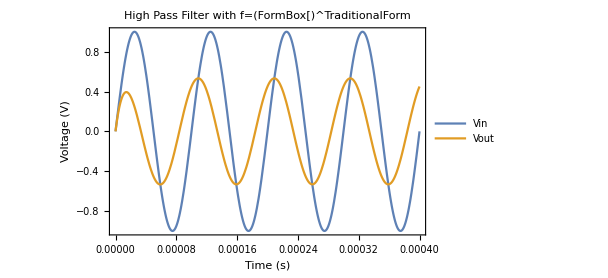

```mathematica
f=10^4;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

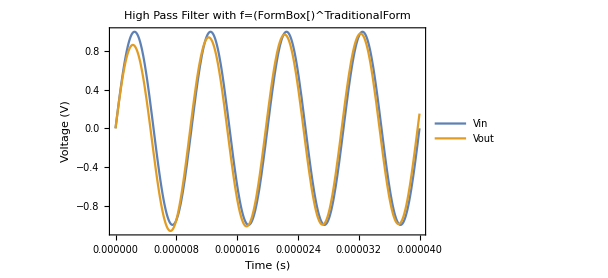

```mathematica
f=10^5;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

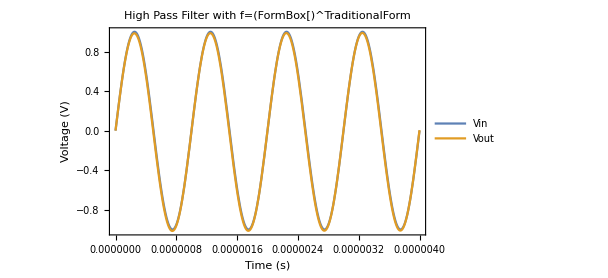

```mathematica
f=10^6;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

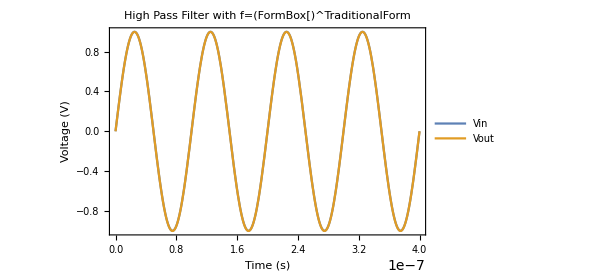

```mathematica
f=10^7;
Plot[{Subscript[V, in][f,Subscript[V, 0],t],Subscript[V, out][f,Subscript[V, 0],t,tau]},{t,0,4/f}, PlotLabel->Style[StringForm["High Pass Filter with f=(`1`s)^-1",ScientificForm[f]],Black,16], Frame->True,FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},PlotLegends->{"Vin",StringForm["Vout"]},PlotRange->All, ImageSize->450]
```

b. Determine the relative (fractional) attenuation of the amplitude as a function of the quotient of cutoff frequency to the input sine wave frequency (i.e. f_cutoff/f_sin). Do not forget to account for the 2π.

This attenuation is given in the text as equation 10.23, (V_(o,m))/(V_(i,m))=R/(√(R^2+1/(2 π f C)^2)). Since the cutoff frequency is given by f_0=1/(2 π R C), if we designate r=f_0/f, we arrive at  (V_(o,m))/(V_(i,m))=R/(√(R^2+(rR)^2))=R/(√(R^2(1+r^2)))=1/(√(1+r^2)).

c. Print out the Mathematica Notebook and turn in the solution with the rest of your prelab assignment.

Here you go!

## Post-Lab

```mathematica
DataFolder=NotebookDirectory[]<>"LAB/";
```

High Pass Filter

Note: Due to experimenter error, the data for the output of the High Pass filter for the square wave input were not saved. In order to complete the assignment, data from another student (Dory Miller) were used to perform the analysis.

```mathematica
HighPassInputFile="DS0031-1.CSV";
HighPassOutputFile = "DS0032-3.CSV";
```

1. Plot the input and output for the square wave investigation on the same plot

```mathematica
HighPassSquareWaveInputData=Multicolumn[Join[Import[DataFolder<>HighPassInputFile][[17;;]][[;;,1]],Import[DataFolder<>HighPassInputFile][[17;;]][[;;,2]]],2]//First;
HighPassSquareWaveOutputData=Multicolumn[Join[Import[DataFolder<>HighPassOutputFile][[17;;]][[;;,1]],Import[DataFolder<>HighPassOutputFile][[17;;]][[;;,2]]],2]//First;
```

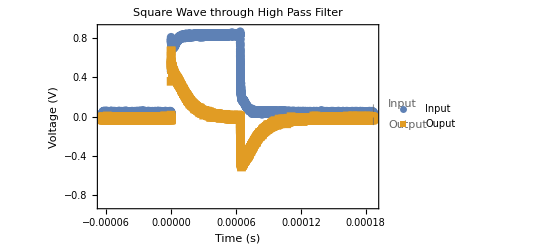

```mathematica
HPSWPlot=ListPlot[{Labeled[HighPassSquareWaveInputData,"Input"],Labeled[HighPassSquareWaveOutputData,"Output"]},
Axes->True,
PlotRange->{{HighPassSquareWaveInputData[[1,1]],HighPassSquareWaveInputData[[-1,1]]},{-0.9,0.9}},
Joined->False,
Frame->True,
FrameLabel->{Style["Time (s)",Black,18],Style["Voltage (V)",Black,18]},
ImageSize->Full,
PlotLabel->Style["Square Wave through High Pass Filter",Black,30],
FrameTicksStyle->Directive[{Black,18},{Black,18}],
PlotMarkers->Automatic,
PlotLegends->Placed[{"Input", "Ouput"},{0.85, 0.85}]
]
```

2. In a text-style cell, quantify what effect the filter had in (1) and if it is what you expected

When the high-pass filter was applied, the effect was to capture primarily the areas where there were rapid changes in the input signal--which is to say the areas where a fourier decomposition would show high frequencies. Areas of the curve where there was little change were filtered out, which is why the output signal drops in the middle of the square wave. In this way the high-pass/CR circuit acts as a crude differentiator, showing a strong positive signal at the rising edge of the square wave and a strong negative signal at the falling edge of the square wave.

3. From the traces collected for the square wave input (csv format), measure the time constant of the network from the collected data and compare to its actual value. Consider equation 5 for this process.

The text gives the time constant τ=RC as the point where a square wave signal has decayed to 40% of the magnitude of the input signal. Using this:

```mathematica
peakVoltage=Max[HighPassSquareWaveOutputData[[;;,2]]]
RCVoltage=ⅇ^-1*peakVoltage
```

0.672

0.247215

From an examination of the raw data in the file “DS0032-3.CSV”, the output of the circuit fades to 0.247V at around 0.0000123s. This compares to the calculated value, τ=RC:

```mathematica
218*0.047*10^-6
```

0.000010246

```mathematica
(%-0.0000123)/%
```

-0.200468

These values therefore agree to within ~20% of each other. The error in measured capacitance was unavailable due to the lack of an appropriate multimeter at the lab station, and the error in resistance (±1Ω) is insufficient to explain this deviation. There is most likely additional systematic error, perhaps from additional capacitance in series with the circuit (perhaps from the coaxial cable).

4. Plot the sine wave results (simulated input and measured output on the same plot) on separate plots at each frequency (5 plots total).

Calculate the magnitude of the input signal:

```mathematica
filename="DS0003.csv";
inputData=Multicolumn[Join[Import[DataFolder<>filename][[17;;]][[;;,1]],Import[DataFolder<>filename][[17;;]][[;;,2]]],2]//First;
Subscript[V, 0]=(Max[inputData[[;;,2]]]-Min[inputData[[;;,2]]])/2;
```

### Input Frequency: 10^3 Hz

```mathematica
filename = "DS0004.csv";
data = Multicolumn[Join[Import[DataFolder<>filename][[17;;]][[;;,1]],Import[DataFolder<>filename][[17;;]][[;;,2]]],2]//First;
f = 10^3; (* Hz *)
inputPlot=Plot[Subscript[V, in][f,1000,t],{t,Min[data[[;;,1]]],Max[data[[;;,1]]]},
PlotStyle->Orange,
PlotRange->Automatic,
PlotLegends->Placed[{"Simulated input"},{0.85,0.85}]
];
dataPlot=ListPlot[
data,
Joined->False,
Frame->True,
ImageSize->Full,
FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},
PlotLabel->Style[StringForm["High Pass Filter with f=`1`Hz",f],Black,30],
PlotLegends->Placed[{"High Pass Output"},{0.85,0.85}],
PlotRange->{{-1/f,1/f},{-1.1*Subscript[V, 0],1.1*Subscript[V, 0]}},
PlotMarkers->{"+"},
FrameTicksStyle->Directive[Black,18]
];
Show[dataPlot,inputPlot]
```

-Graphics-

### Input Frequency: 10^4 Hz

```mathematica
filename = "DS0005.csv";
data = Multicolumn[Join[Import[DataFolder<>filename][[17;;]][[;;,1]],Import[DataFolder<>filename][[17;;]][[;;,2]]],2]//First;
f = 10^4; (* Hz *)
inputPlot=Plot[Subscript[V, in][f,1000,t],{t,Min[data[[;;,1]]],Max[data[[;;,1]]]},
PlotStyle->Orange,
PlotRange->Automatic,
PlotLegends->Placed[{"Simulated input"},{0.85,0.85}]
];
dataPlot=ListPlot[
data,
Joined->False,
PlotMarkers->{"+"},
Frame->True,
ImageSize->Full,
FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},
PlotLabel->Style[StringForm["High Pass Filter with f=`1`Hz",f],Black,30],
PlotLegends->Placed[{"High Pass Output"},{0.85,0.85}],
PlotRange->{{-1/f,1/f},{-1.1*Subscript[V, 0],1.1*Subscript[V, 0]}},
FrameTicksStyle->Directive[Black,18]
];
Show[dataPlot,inputPlot]
```

-Graphics-

### Input Frequency: 10^5 Hz

```mathematica
filename = "DS0006.csv";
data = Multicolumn[Join[Import[DataFolder<>filename][[17;;]][[;;,1]],Import[DataFolder<>filename][[17;;]][[;;,2]]],2]//First;
f = 10^5; (* Hz *)
inputPlot=Plot[Subscript[V, in][f,1000,t],{t,Min[data[[;;,1]]],Max[data[[;;,1]]]},
PlotStyle->Orange,
PlotRange->Automatic,
PlotLegends->Placed[{"Simulated input"},{0.85,0.85}]
];
dataPlot=ListPlot[
data,
Joined->False,
PlotMarkers->{"+"},
Frame->True,
ImageSize->Full,
FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},
PlotLabel->Style[StringForm["High Pass Filter with f=`1`Hz",f],Black,30],
PlotLegends->Placed[{"High Pass Output"},{0.85,0.85}],
PlotRange->{{-1/f,1/f},{-1.1*Subscript[V, 0],1.1*Subscript[V, 0]}},
FrameTicksStyle->Directive[Black,18]
];
Show[dataPlot,inputPlot]
```

-Graphics-

### Input Frequency: 10^6 Hz

```mathematica
filename = "DS0007.csv";
data = Multicolumn[Join[Import[DataFolder<>filename][[17;;]][[;;,1]],Import[DataFolder<>filename][[17;;]][[;;,2]]],2]//First;
f = 10^6; (* Hz *)
inputPlot=Plot[Subscript[V, in][f,1000,t],{t,Min[data[[;;,1]]],Max[data[[;;,1]]]},
PlotStyle->Orange,
PlotRange->Automatic,
PlotLegends->Placed[{"Simulated input"},{0.85,0.85}]
];
dataPlot=ListPlot[
data,
Joined->False,
Frame->True,
ImageSize->Full,
FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},
PlotLabel->Style[StringForm["High Pass Filter with f=`1`Hz",f],Black,30],
PlotLegends->Placed[{"High Pass Output"},{0.85,0.85}],
PlotRange->{{-1/f,1/f},{-1.1*Subscript[V, 0],1.1*Subscript[V, 0]}},
PlotMarkers->{"+"},
FrameTicksStyle->Directive[Black,18]
];
Show[dataPlot,inputPlot]
```

-Graphics-

### Input Frequency: 10^7 Hz

```mathematica
filename = "DS0008.csv";
data = Multicolumn[Join[Import[DataFolder<>filename][[17;;]][[;;,1]],Import[DataFolder<>filename][[17;;]][[;;,2]]],2]//First;
f = 10^7; (* Hz *)
inputPlot=Plot[Subscript[V, in][f,1000,t],{t,Min[data[[;;,1]]],Max[data[[;;,1]]]},
PlotStyle->Orange,
PlotRange->Automatic,
PlotLegends->Placed[{"Simulated input"},{0.85,0.85}]
];
dataPlot=ListPlot[
data,
Joined->False,
Frame->True,
ImageSize->Full,
FrameLabel->{Style["Time (s)",Black,16],Style["Voltage (V)",Black,16]},
PlotLabel->Style[StringForm["High Pass Filter with f=`1`Hz",f],Black,30],
PlotLegends->Placed[{"High Pass Output"},{0.85,0.85}],
PlotRange->{{-1/f,1/f},{-1.1*Subscript[V, 0],1.1*Subscript[V, 0]}},
PlotMarkers->{"+"},
FrameTicksStyle->Directive[Black,18]
];
Show[dataPlot,inputPlot]
```

-Graphics-

5. For the sine wave, determine the relative (fractional) attenuation of the amplitude as a function of the quotient of cutoff frequency to the input sine wave frequency (i.e., f_cut/f_sine). Do not forget to account for the 2π.

15533.4

{0.00138902,0.00138902,0.0138902,0.0138902,0.0138902}

0.666667

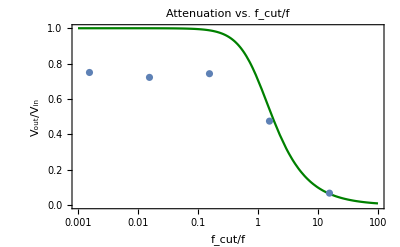

```mathematica
freqarray={10^3,10^4,10^5,10^6,10^7};
fcutoff=(2*π*0.047*10^-6*218)^-1
freqquotient=fcutoff/freqarray;
outputMagnitudes={0.980,6.84,10.7, 10.4, 10.8}/(2*Subscript[V, 0]);
measurementErrors={0.01,0.01,0.1,0.1,0.1};
outputErrors=√((measurementErrors/Subscript[V, 0])^2+(-measurementErrors/Subscript[V, 0]^2*0.1)^2)
data=Multicolumn[Join[freqquotient,outputMagnitudes],2]//First;
dataPlot=ListLogLinearPlot[data,
PlotLegends->Placed[{"Measured"},{0.85,0.85}]];
theoryPlot=LogLinearPlot[1/√(1+r^2),{r,0.001,100},
ImageSize->Full,
Frame->True,
FrameLabel->{Style["f_cut/f",Black,24],Style["V_out/V_in",Black,24]},
PlotLabel->Style["Attenuation vs. f_cut/f",Black,30],
PlotStyle->Darker[Green,0.5],
PlotLegends->Placed[{"Theoretical prediction"},{0.85,0.85}],
FrameTicksStyle->Directive[Black,18]];
Subscript[V, 0]/10.8
Show[theoryPlot,dataPlot]
```

6. In a text-style cell, compare the results in (5) to the analytical solution from the prelab and quantify and discrepancies and where they may have come from.

Quantified Discrepancies:

```mathematica
freqquotient
Abs[1/√(1+freqquotient^2)-data[[;;,2]]]/(1/√(1+freqquotient^2))
-outputMagnitudes
data[[;;,2]]
```

{15.5334,1.55334,0.155334,0.0155334,0.00155334}

{0.0593207,0.122489,0.248033,0.277691,0.249999}

{-0.0680556,-0.475,-0.743056,-0.722222,-0.75}

{0.0680556,0.475,0.743056,0.722222,0.75}

The measured values follow the form of the predicted curve very closely. The magnitudes do not match accurately, however, with even the high-frequency signals appearing to be attenuated by a factor of approximately 2/3. This is likely due to components of the breadboard and lengthy coaxial cable acting as a resistor divider of sorts and attenuating the signal by this factor. Alternatively, a low pass filter formed by the capacitance inherent in the coaxial cable. Wikipedia (https://en.wikipedia.org/wiki/Coaxial_cable) provides an equation for the cutoff frequency for a coaxial cable:
f_c≈1/(π((D+d)/2)√μϵ)
Without knowing the specific parameters of the cable in question, it is impossible to verify if this cutoff frequency corresponds with the measured output. However, it seems likely that if the capacitor was acting as an additional filter it would have frequency dependence that is not apparent in the plot. The errors in the frequency generator were treated as 0 for the purposes of propagation. Errors in the ratio of measured voltage to input voltage were not plotted due to the scale of the plot. 
While this seems to visually resemble figure 10.12 from the text (depicting the output of a lowpass filter), this is due to the fact that the abscissa is f_cut/f--the inverse of the f/f_0 in figure 10.12

The actual values varied from the calculated values by a factor depending on the frequency.

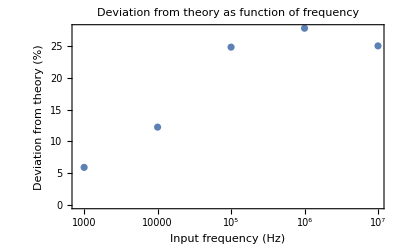

```mathematica
ListLogLinearPlot[Multicolumn[Join[freqarray,100*Abs[1/√(1+freqquotient^2)-data[[;;,2]]]/(1/√(1+freqquotient^2))],2]//First,
PlotRange->All, ImageSize->Full,Frame->True,FrameLabel->{Style["Input frequency (Hz)",Black,20],Style["Deviation from theory (%)",Black,20]}, PlotLabel->Style["Deviation from theory as function of frequency",Black,30],FrameTicksStyle->Directive[Black,18]]
```

Low Pass Filter

```mathematica
LowPassInputFile="DS0009.CSV";
LowPassOutputFile = "DS0010.CSV";
```

1. Plot the input and output for the square wave investigation on the same plot

```mathematica
LowPassSquareWaveInputData=Multicolumn[Join[Import[DataFolder<>LowPassInputFile][[17;;]][[;;,1]],Import[DataFolder<>LowPassInputFile][[17;;]][[;;,2]]],2]//First;
LowPassSquareWaveOutputData=Multicolumn[Join[Import[DataFolder<>LowPassOutputFile][[17;;]][[;;,1]],Import[DataFolder<>LowPassOutputFile][[17;;]][[;;,2]]],2]//First;
```

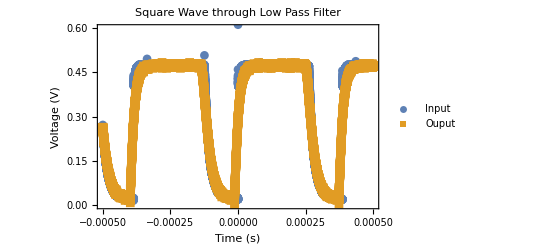

```mathematica
LPSWPlot=ListPlot[{LowPassSquareWaveInputData,LowPassSquareWaveOutputData},
Axes->True,
PlotRange->{{LowPassSquareWaveInputData[[1,1]],LowPassSquareWaveInputData[[-1,1]]},{0,0.6}},
Joined->False,
Frame->True,
FrameLabel->{Style["Time (s)",Black,18],Style["Voltage (V)",Black,18]},
ImageSize->Full,
PlotLabel->Style["Square Wave through Low Pass Filter",Black,30],
FrameTicksStyle->Directive[{Black,18},{Black,18}],
PlotMarkers->Automatic,
PlotLegends->Placed[{"Input", "Ouput"},{0.85, 0.85}]
]
```

2. In a text-style cell, quantify what effect the filter had in (1) and if it is what you expected

When the low pass filter was applied, the high frequencies that contribute to the sharp “corners” of the square wave are attenuated, while the low frequencies that make up the flat portions of the curve are not attenuated and are therefore left at the same level. This has the effect of transforming the square pulses into more rounded shapes. The longer the time constant, τ=RC grows, the more this circuit would resemble an integrator (while the square wave is “high”). After the square wave ends, the pulse decays as the capacitor releases its accumulated charge to the circuit output.

3. From the traces collected for the square wave input (csv format), measure the time constant of the network from the collected data and compare to its actual value. Consider equation 5 for this process.

Find the minimum voltage, then the maximum voltage, then the value when voltage is V_min+ⅇ^-1 V_max.10. Figure out the time, and that should represent the time constant.

```mathematica
MaxVoltage=0.472;
MinVoltage=0.02;
deltaVoltage=MaxVoltage-MinVoltage;
MinVoltage+Exp[-1]*deltaVoltage
```

0.186282

The voltage rises to this level at time t=--0.00039168s, while the pulse started at -4E-4s.

```mathematica
-0.00039168-(-4*10^-4)
```

8.32×10^-6

The measured time constant for this circuit is therefore 8μs. This is relatively close to the calculated value of

4. For the sine wave, determine the relative (fractional) attenuation of the amplitude as a function of the quotient of cutoff frequency to the input sine wave frequency (i.e., f_cut/f_sine). Do not forget to account for the 2π.

Note: due to some undiagnosed error, likely in the signal generator, the specific frequency of 10^6 Hz appeared completely attenuated (see plot above). This occurred using different breadboards, cables, and circuit components. Since the other frequencies were unaffected, I have decided not to replace the data for this specific frequency, and to attempt to determine the relationship using the other four data pairs.

```mathematica
freqarray={10^3,10^4,10^5,10^7};
fcutoff=(2*π*0.047*10^-6*218)^-1;
freqquotient=fcutoff/freqarray
outputMagnitudes={14.0,10.7,1.76, 3.64*10^-3}/(2*Subscript[V, 0])
data=Multicolumn[Join[freqquotient,outputMagnitudes],2]//First;
dataPlot=ListLogLinearPlot[data,
Frame->True,
FrameTicksStyle->Directive[Black,16],
FrameLabel->{Style["f_cut/f",Black,20], Style["V_out/V_in",Black,20]},
PlotLabel->Style["Attenuation vs f_cut/f",Black,30],
ImageSize->Full,
PlotLegends->Placed[{"Observed"},{0.15,0.85}]];
```

{15.5334,1.55334,0.155334,0.00155334}

{0.972222,0.743056,0.122222,0.000252778}

The attenuation values for the ratio of cutoff frequency to input frequency are reported and plotted above.

5. In a text-style cell, compare the results in (4) to the analytical solution from the prelab and quantify any discrepancies and where they may have come from.

In the prelab we solved for the relationship between V_0/V_i and f_cut/f_sine for a CR/high pass circuit, not an RC/low pass circuit. In the case of a low pass circuit, the applicable relationship is given in the text as equation 10.26:
V_0/V_i=(1/(ωC))/(√(R^2+1/(ωC)^2))=(1/(2πfC))/(√(R^2+1/(2πfC)^2))
Substituting f_cut=1/(RC) -> f_cut/f=1/(2πfRC)=r into the equation above:
V_0/V_i=(1/(ωC))/(R √(1+1/(ωRC)^2))=(1/(2πfRC))/(√(1+1/(2πfRC)^2))=r/(√(1+r^2))

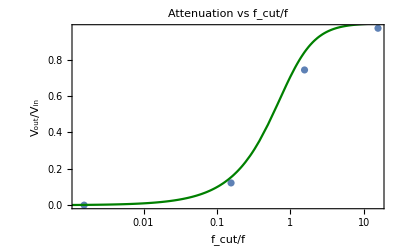

```mathematica
theoryPlot=LogLinearPlot[r/√(1+r^2),{r,0.001,1000},
PlotLegends->Placed[{"Theoretical"},{0.15,0.85}],
PlotStyle->Darker[Green,0.5]];
Show[dataPlot,theoryPlot]
```

These two plots agree very closely (once again, error bars omitted due to small magnitudes). While the small number of data points make it hard to determine if the same attenuation factor is applicable at high frequencies. Still, the data points as measured show good agreement with equation 10.26 from the text. Because this is a plot of f_cut/f rather than the inverse, the picture does not resemble figure 10.12 from the text.